Power::infy: 碰到无穷表达式 1/0..

Power::infy: 碰到无穷表达式 1/0.^2.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

NDSolve::ndnum: 在 r == 0. 处碰到一个导数的非数值量.

NDSolve::berr: 9.12586×10^7 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 0. 处碰到一个导数的非数值量.

NDSolve::berr: 1.70646×10^7 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

NDSolve::ndnum: 在 r == 0. 处碰到一个导数的非数值量.

General::stop: 在本次计算中，NDSolve::ndnum 的进一步输出将被抑制.

NDSolve::berr: 3.7227×10^7 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，NDSolve::berr 的进一步输出将被抑制.

$Aborted

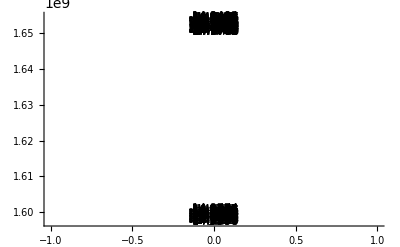

```mathematica
V[r_]:=-1/r
data={};txt={};
r1=1;r2=10^-6;u[r1]=10^-6;
n=100;δ=0.02/n;
Do[
equ={u''[r]+(2(Ε-V[r])-2/r^2)u[r]==0,u[r2]==0,u'[1]==√(2(V[r1]-Ε)) 10^-6};
s=NDSolve[equ,u,{r,r1,r2}];
U=u/.s[[1]];
total=NIntegrate[U[r]^2,{r,r1,r2}];
g=Plot[U[r]/(√total),{r,r1,r2},
PlotRange->{{r1,1.3r2},All}];
AppendTo[data,g];
AppendTo[txt,Text[ToString[Ε],{1.13r2,U[r2]/total}]],
{Ε,-15,0,δ}]
Show[data,Graphics[txt],
AxesOrigin->{0,0},AxesLabel->{"r","u"}]
Clear["Global`*"]
```